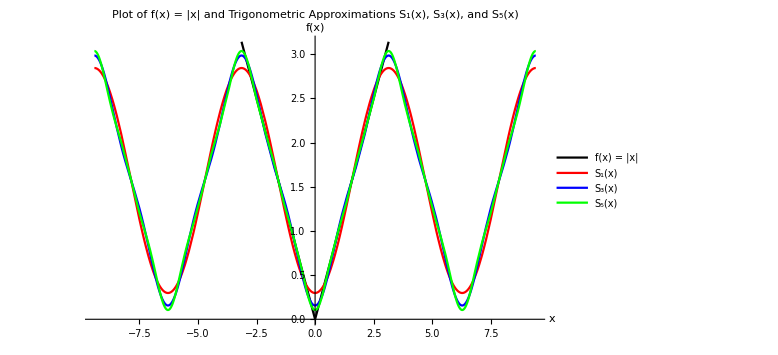

```mathematica
plot1 = Plot[Abs[x],{x,-3*Pi,3*Pi},PlotStyle->Black, PlotRange->{0,Pi}];
plot2 = Plot[Pi/2 -4/Pi*Cos[x],{x,-3*Pi,3*Pi}, PlotStyle->Red];
plot3 = Plot[Pi/2 -4/Pi*Cos[x] - 4/(9*Pi)*Cos[3*x],{x,-3*Pi,3*Pi}, PlotStyle->Blue];
plot4 = Plot[Pi/2 -4/Pi*Cos[x] - 4/(9*Pi)*Cos[3*x] - 4/(25*Pi)*Cos[5*x],{x,-3*Pi,3*Pi}, PlotStyle->Green];
legend = LineLegend[{Black,Red,Blue,Green},{"f(x) = |x|", "S_1(x)", "S_3(x)","S_5(x)"}];
Legended[Show[plot1,plot2,plot3,plot4, PlotLabel->"Plot of f(x) = |x| and Trigonometric Approximations S_1(x), S_3(x),  and S_5(x)", AxesLabel-> {"x","f(x)"},ImageSize->Large],legend]
```

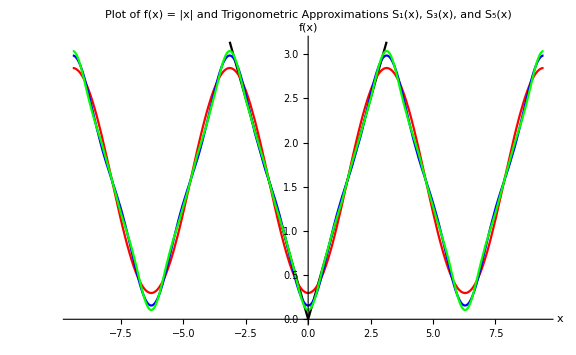

```mathematica
Show[plot1,plot2,plot3,plot4, PlotLabel->"Plot of f(x) = |x| and Trigonometric Approximations S_1(x), S_3(x),  and S_5(x)", AxesLabel-> {"x","f(x)"},ImageSize->Large,PlotLegends->Automatic]
```